# Rosseller: Sections

## Rosseller System, Sensitivity, and Sections

We are going to build code and explore the behavior of the system on the standard section.

### Existing Code Fragments

#### Version 1

Right now we know how to go round a bunch of times recording stuff as we cross the Poincare section. I added the sensitivity computation.

-Graphics3D-

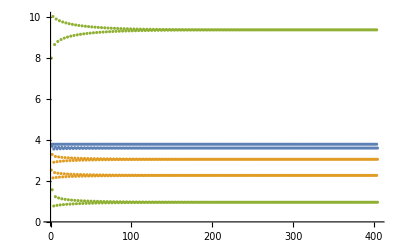

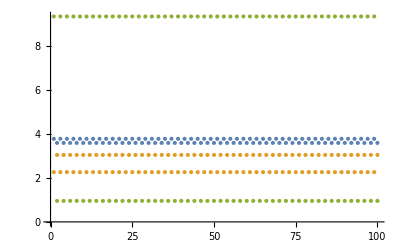

{{{3.78865,2.26831,9.36663},{{-0.363768,-4.28398,-0.356502},{0.132638,1.56202,0.129986},{-9.61282×10^-6,-0.0000235543,1.4671×10^-6}}},{{3.60131,3.0536,0.958366},{{-0.12543,-1.4772,-0.12293},{0.131688,1.55086,0.129059},{2.79438×10^-6,4.0592×10^-6,-7.65047×10^-7}}},{{3.78865,2.2683,9.36672},{{-0.363767,-4.284,-0.356504},{0.132633,1.56201,0.129987},{8.65902×10^-6,0.0000163852,-1.90835×10^-6}}},{{3.60131,3.05359,0.95834},{{-0.125436,-1.4772,-0.122927},{0.13169,1.55086,0.129058},{-3.08519×10^-6,-8.79263×10^-6,3.21116×10^-7}}}}

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
yJData=Reap[
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}
]]⟦2,1⟧;
ParametricPlot3D[ySol[t],{t, 0.9*TMax, TMax},PlotRange->All]
ListPlot[yJData⟦All,1⟧ᵀ,PlotRange->All]
ListPlot[yJData⟦-100;;-1,1⟧ᵀ,PlotRange->All]
yJData⟦-4;;-1⟧
```

#### Version 2

I can do the data extraction in a different way. If we want.

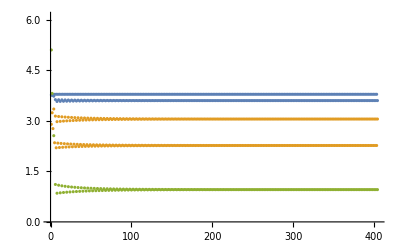

{{3.60131,3.05359,0.958342},{{1.24157,2.23782,-0.169391},{-1.30363,-2.34961,0.177864},{-0.000159545,-0.000201256,0.0000274521}}}

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={PData,{y[t],J[t]}})
}
];
PData=Partition[Flatten[PData],3+3^2];
PData=Table[yJs=PData⟦i⟧;
ys=yJs⟦1;;3⟧; Js=yJs⟦4;;3+3^2⟧;
{ys,Partition[Js,3]},{i,Length[PData]}];
yData=PData⟦All,1⟧;
ListPlot[yDataᵀ]
{yEnd, JEnd}=PData⟦-1⟧
```

```mathematica
MatrixForm[JEnd];
MatrixForm[JEndᵀ.JEnd];
MatrixForm[JEnd.JEndᵀ];
Eigenvalues[JEnd];
SingularValueList[JEnd,Tolerance->0]
```

{3.71885,0.0000506189,1.08826×10^-16}

#### Version 3

We also know how to go round once and stop the first time we cross the P-section.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=234; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={y[t],J[t]};"StopIntegration")
}
];
PData
```

{{3.77082,2.89763,5.10453},{{-0.0570967,1.85847,0.029455},{0.450972,-0.350306,-0.102516},{-3.23243,-3.22319,0.457328}}}

### Code Development

The plan is to build up code to recreate bettre versions of the images from Wiki.  For example, https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor#Varying_a

### Basic ODE Solver Tests: Speed

Seeing if we can make the basic solve a tad faster. I do not think 5% is worth the fuss.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},{y,J},{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}];
]
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}];
]
AbsoluteTiming[
Quiet[NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},{},{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}]];
]
```

{2.09434,Null}

{2.00506,Null}

{1.98554,Null}

The code might be faster as the more explicit x,y,z version of the code.  It might be faster with the parameters passed in to functions.  I think it will be faster if we do not do the sensitivity computation on the approach to asymptotic version.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[y[t]]
}];
]
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[y[t]]
}];
]
```

{1.17311,Null}

{1.15986,Null}

It is faster but not as much faster as I might have hoped. I do not think changing the saving technique would change much.  It might get faster changing the ODE algorithm but I think that is getting a bit distracted.

If I really wanted this to be as fast as possible I would implement it in Julia with the update variables stored as static following the advice in the Julia documentation.  I think this would produce some real speed up.  I do not know how the Julia event handler would interact with the optimizations.

Conclusions: 1) Stick with Mathematica. 2) Drop the sensitivity Analysis for getting to the limit cycle. 3) Do not worry to much about the solver.

### Code Chunks

#### SetUpSection

Making it stop after “SetUpCount” crossings of standard section “z” at max.
Input: f as a suitable function, t0 IC 3-vector and and SetUpCount.  
Output: list of counter, end time, and final crossing point 3-vector.
I am not going to bother “typing” the variables.

```mathematica
SetUpSection[f_,y0_,SetUpCount_]:=Module[
{n=0,y,t,TMax=10^4,yOut,tOut=0.0},
NDSolveValue[{
y'[t]==f[y[t]],
y[0]==y0
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(
If[n++>SetUpCount,tOut=t;yOut=y[t];"StopIntegration"]
)
}];
{n,tOut,yOut}
]
```

Here is a timed test of the development version.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
 p={0.2,0.2,3.81};
y0={3,4,5};
Table[
AbsoluteTiming[SetUpSection[f[p],y0,SetUpCount]],
{SetUpCount,{100,101,1000,1001}}]
```

{{0.342036,{102,589.702,{3.60445,3.06308,0.973017}}},{0.299225,{103,595.677,{3.78874,2.26026,9.40922}}},{2.7431,{1002,5796.28,{3.60131,3.05359,0.958349}}},{2.68743,{1003,5802.26,{3.78865,2.2683,9.36667}}}}

Has it converged?

Could we help it converge faster?

Is there any danger in helping it converge faster?

#### StepRoundSection

Once we have found a limit cycle we need to make the solver step round the limit cycle until it gets back to the same point and save a list of crossing points and sensitivities?  I do not think we have any idea right now about how close a return point needs to be:  we decided to call the return tolerance “DyTol”.  For safety we need to make a maximum number of loops: we decided to call that MaxCounts. It needs to take as input the function, the sensitivity function, and the initial point.  I think we decided it should return a list of counts, times, points, and sensitivities.

```mathematica
StepRoundSection[{f_,df_},y0_,MaxCounts_]:=Module[
{n=0,y,J,t,TMax=10^4,yOut,tOut=0.0},
Reap[NDSolveValue[{
y'[t]==f[y[t]],
J'[t]==df[y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(
Sow[{n++,t,y[t],J[t]}];
If[n>MaxCounts,"StopIntegration"]
)
}]]⟦2,1⟧
]
```

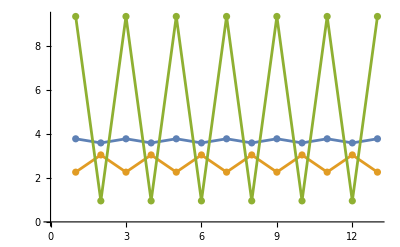

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
 p={0.2,0.2,3.81};
y0={3,4,5};
SetUpCount=1000;
MaxCounts=12;
{n,t,ySection}=SetUpSection[f[p],y0,SetUpCount];
Data=StepRoundSection[{f[p],df[p]},ySection,MaxCounts];
xyzs=Data⟦All,3⟧;
ListPlot[
xyzsᵀ,
Joined->True,Mesh->All
]
zs=xyzs⟦All,3⟧;
ListPlot[zs,Joined->True,Mesh->All]
ListPlot[zs⟦1;;MaxCounts;;2⟧,Joined->True,Mesh->All]
```

Has it converged?

How/where do we put a stopping condition in our code?

What should our tolerance be?

Is there any danger in setting a low tolerance?

Does it matter if it is a relative or absolute tolerance?